```mathematica
datlM={100000,83641,78263,75435,73685,72372,71388,70616,69969,69435,68986,68598(*68598*),68251,67926,67606,67278,66930,66553,66140,65687(*65697*),65190,64650,64103,63549,62988(*6292(8)8*),62422,61850,61273,60691,60103,59509,58909,58304,57691,57072,56444,55808,55163,54508,53842,53166,52475,51773,51057,50325,49577,48813,48031,47231,46411,45573,44714,43810,42880(*4283(8)0*),41926,40946,39941,38909,37848,36737,35633,34474,33279,32045,30772,29456,28106,26716,25290,23833,22349,20845,19330,17811,16300,14808,13345,11925,10559,9257,8034,6895,5847,4827,4047,3298,2648,2093,1627,1243,932,686,495,349,241,160,107,69,43,25,15};
datlF={100000,86599,81117,78289,76416,75055,74053,73277,72612,72054(*72(10)(35)4*),71578,71158(*71153*),70777,70416,70059(*70059*),69692(*696(29)2*),69305,68889(*688(58)9*),68438,67946,67412,66834,66247,65651(*65631*),65046,64434(*64424*),63815,63189(*63159*),62558,61920(*61820*),61277,60630,59977,59320,58657,57992(*57822*),57318,56643,55962,55277,54584(*54554*),53888,53184,52476,51762,51041,50312,49577,48834,48089,47324,46557,45781,44997,44203,43333,42424,41476,40490,39464,38397,37300,36139,34944,33703,32416,31083,29705,28282,26818,25316,23782,22223,20646,19062,17480,15912,14372,12871,11423,10039,8732,7512,6386,5362,4442,3628,2920,2312,1803,1380,1038,765,553,391,270,183,120,77,48,30};
```

```mathematica
datlM[[53;;60]]
```

{43810,42830,41926,40946,39941,38909,37848,36737}

```mathematica
datlM[[53+1]]+40
```

42870

```mathematica
datlM[[24+1]]
```

62988

```mathematica
datlF[[15]]
```

70059

22

33

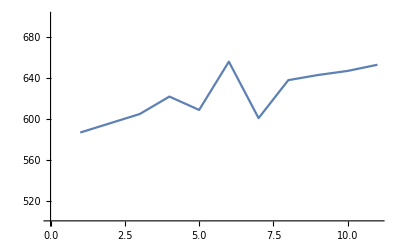

```mathematica
min=22
max=33
ListPlot[(-Differences@datlF[[min;;max]]),PlotRange->{500,700},Joined->True]
```

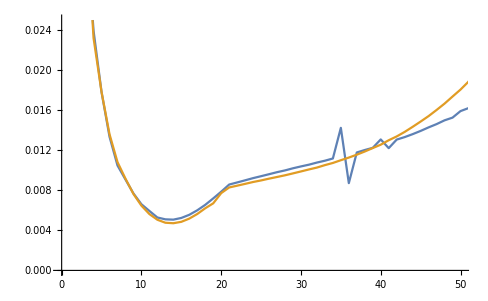

```mathematica
ListPlot[
{(-Differences@datlF)/datlF[[;;-2]],
(-Differences@datlM)/datlM[[;;-2]]}
,PlotRange->{{0,50},{0,.025}},Joined->True]
```